# Graph Thickness: Effectiveness of Randomized Algorithms

## Sean Adams, Scott Meyer, Sean Meyer

## Outline

Theoretical upper bounds on thickness for each graph

Research into known algorithms and techniques for finding thickness

Our thickness algorithm

Results for competition graphs

Comparison of our results to previous results

## Theoretical Upper Bounds

We came across several formulas1 for thickness that we combined to calculate an upper bound on thickness, in order to have something to judge our results against.

### Formulas

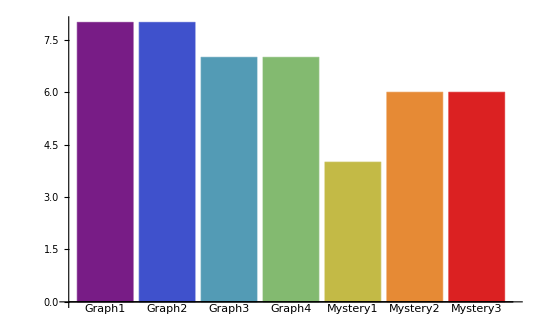
If G = (V,E) is a graph with |V| >10, |E|=m, max degree = d then:
θ(G) ≤ ⌊√(e/3)+7/6⌋
θ(G) ≤ ⌈d/2⌉

Thus upper bound = Min[ ⌊√(e/3)+7/6⌋ , ⌈d/2⌉ ]
-Graphics-

## Research

Here is what we found from our research:

A common, and reasonably effective, heuristic approach to finding thickness is to extract maximal planar subgraphs until the resulting graph is planar (Mutzel, Odenthal, & Scharbrodt, 1998).

Definition: A maximal planar subgraph is a planar subgraph for which the addition of even one more edge creates an edge crossing.

Somewhat surprisingly, a naive random algorithm is actually very effective at finding good maximal planar subgraphs (Chimani, Klein, & Wiedera, 2016).

### Effectiveness of Random (Nï) Algorithm for Maximal Planar Subgraphs -Graphics- -Graphics-

These graphs, taken from Chimani et al. (2016), show two things about this algorithm:

It's effective at finding dense planar subgraphs

Those subgraphs minimize edge crossings when the remaining edges are added back in

While a random algorithm produces very good results for density and edge crossings, we didn’t find any instances of this algorithm being used to calculate thickness. Based on this, we decided to test how it would perform for thickness—for both a single run and over a prolonged period.

## Our Algorithm

### Thickness

Input: graph G = (V, E)
	Output: thickness of G
	begin
		t = 1
		while G is not planar
			t = t + 1
			G’ = maximal planar subgraph of G
			E’ = edges of G’
			G = G(E\E’)
		return t
	end

### Maximal Planar Subgraph

Input: graph G = (V, E)
	Output: maximal planar subgraph
	begin
		edges = shuffle(E)
		subgraph = (V, ∅)
		for each edge of edges
			temp = subgraph + edge
			if temp is planar
				subgraph = temp
		return subgraph
	end

## Results for Competition Graphs

Below shows the thickness values we got for each graph, both after running the random algorithm once and for 3 hours.

Graph | 1 Run | 3 Hours | Upper Bound
K5 | 2 | _ | 2
K8 | 2 | _ | 2
K9 | 3 | _ | 3
Graph1 | 3 | 3 | 8
Graph2 | 3 | 3 | 8
Graph3 | 3 | 3 | 7
Graph4 | 3 | 3 | 7
MysteryGraph1 | 3 | 2 | 4
MysteryGraph2 | 3 | 3 | 6
MysteryGraph3 | 3 | 3 | 6

Since the values for most of the graphs are unknown we can’t be sure how accurate these numbers are, but we did definitely get the correct value at least for Mystery Graph 1. The others are all either correct or off by just one, so we are quite pleased with the results. Random variations did result in improvement for one graph, but not on any of the others.

### Thickness 2 Embedding for Mystery Graph 1

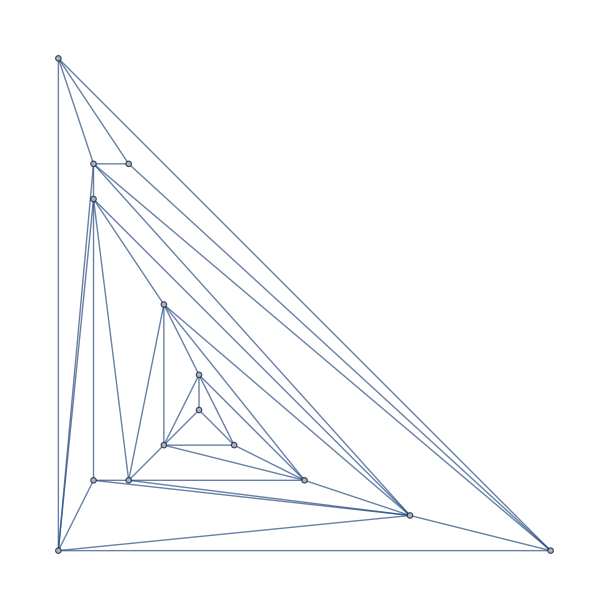
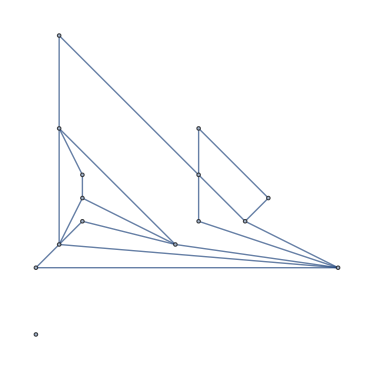

## Comparison to Previous Results

Since we don't know the actual thickness values for the competition graphs, we also compared our results to previous findings in the literature (Mutzel et al., 1998).

```mathematica
{{Graph, 1 Run, 3 Hours, Literature Results, Theoretical}, {K15, 4, 3, 4, 3}, {K20, 5, 5, 5, 4}, {K25, 6, 6, 6, 5}, {K30, 7, 7, 7, 6}, {K35, 8, 8, 8, 7}, {K40, 9, 9, 9, 7}}
```

## Conclusion

The random maximal solution is very fast, but not great at finding optimal solutions, especially on large graphs.

### Maximal

Part of the problem with our solution was how heavily it relies on maximal planar subgraphs. Sometimes, the optimal solution does not include a maximum planar subgraph.
-Graphics-
This graph is entirely planar except for a K_(3,3) on {8,12,14,31,33,37}.
The maximum planar subgraph is just this graph with the K_(3,3) removed. You then need 2 more subgraphs to make the K_(3,3) planar.

However, this graph can be made planar with only two subgraphs, neither of which is the maximum.
-Graphics-

### Utilizing Randomization and Maximal

The best part about our solution was how quickly it could generate ‘pretty good’ results. Slower solutions may be able to utilize our solution inside loops.

### Possible Solution to Maximal Problem

If you could identify all K_5 and K_(3,3) subgraphs and remove all edges not included in these subgraphs, you could then run our solution over the remaining edges. Once that produces results you should be able to add all removed edges back into the produced subgraphs.

This would solve the above maximal problem, while allowing you to use our simple fast solution.

4. A simple path  with n vertices (n>1), written P_n, is given by P_n=(V(P_n), E(P_n)), where

V(P_n)={1,2,3,…,n} and

E(P_n)={(i,i+1): 1≤i≤n-1}.

We write P_n=v_1…v_n, where v_iv_(i+1)∈E(P_n) for i=1,…,n-1.

```mathematica
Manipulate[PathGraph[Range[i]],{i,2,15,1}]
```

### References

P. Mutzel, T. Odenthal, and M. Scharbrodt. The thickness of graphs : a survey. Graphs and Combinatorics, 14 : 59–73, 1998.

Chimani M., Klein K., Wiedera T. (2016) A Note on the Practicality of Maximal Planar Subgraph Algorithms. In : Hu Y., Nöllenburg M. (eds) Graph Drawing and Network Visualization. GD 2016. Lecture Notes in Computer Science, vol 9801.